-Graphics-

# New in Wolfram Language 12.2

## Visualization & Graphics

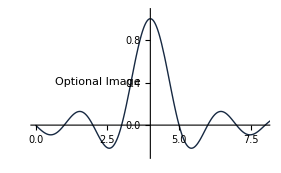

## Topic Overview

### New Graphics Filling Directives

#### LinearGradientFilling

#### RadialGradientFilling

#### ConicGradientFilling

### More Updates for Vector Visualization

#### SliceVectorPlot3D

#### StreamPlot

### New Array Visualization Functions

#### ArrayPlot3D

#### ComplexArrayPlot

### New Multidimensional Plotting Functions

#### RadialAxisPlot

#### ParallelAxisPlot

### PointValuePlot

## New Graphics Filling Directives

Wolfram Language 12.2 includes three new graphics directives that implement different forms of gradient filling.

### LinearGradientFilling

The simplest filling directive is LinearGradientFilling, which interpolates between colors going in a constant direction:

```mathematica
Graphics[{LinearGradientFilling[{Red,Blue}],}]
```

-Graphics-

You can change the direction the gradient fills in:

```mathematica
Graphics[{LinearGradientFilling[{Red,Blue},5Pi/4],}]
```

-Graphics-

### RadialGradientFilling

RadialGradientFilling fills out from a central point:

```mathematica
Graphics[{RadialGradientFilling[{Red,Blue}],}]
```

-Graphics-

### ConicGradientFilling

ConicGradientFilling fills the color through the angles in a circle instead of through the radius:

```mathematica
Graphics[{ConicGradientFilling[{Red,Blue}],}]
```

-Graphics-

### Applications

You can use the new filling directives as styles in visualization functions just like you would use a normal color:

```mathematica
Plot[Sin[x]+x,{x,0,20},Filling->Axis,FillingStyle->LinearGradientFilling[{Pink,Blue},Top]]
```

-Graphics-

```mathematica
BarChart[{2,3,6,9,10,13},ChartStyle->LinearGradientFilling[{Pink,Blue},Top]]
```

-Graphics-

## More Updates for Vector Visualization

The appearance of the vector plotting functions has been updated over the past few years, and the biggest change has been to use color instead of size to indicate the strength of the vector field. In Wolfram Language 12.2, those changes also apply to SliceVectorPlot3D, StreamPlot and related functions.

### SliceVectorPlot3D

```mathematica
Grid[{{-Graphics3D-,SliceVectorPlot3D[{y,-x,z}, "CenterPlanes",{x,-2,2},{y,-2,2},{z,-2,2},PlotLabel->Style["New","Subsection",RGBColor[0.8,0.1,0.1]],ImageSize->400]}}]
```

-Graphics3D- | -Graphics3D-

### StreamPlot

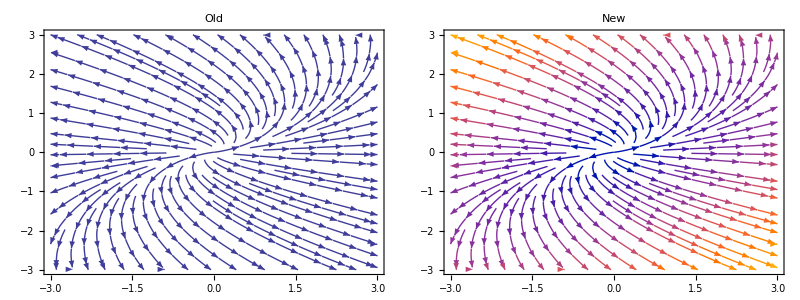

```mathematica
Grid[{{StreamPlot[{x-y,y},{x,-3,3},{y,-3,3},PlotTheme->"ClassicColor",PlotLabel->Style["Old","Subsection",Darker@Gray],ImageSize->400],StreamPlot[{x-y,y},{x,-3,3},{y,-3,3},PlotLabel->Style["New","Subsection",RGBColor[0.8,0.1,0.1]],ImageSize->400]}}]
```

## New Array Visualization Functions

### ArrayPlot3D

ArrayPlot3D is a 3D version of ArrayPlot, useful for visualizing the evolution of 2D cellular automata or individual states of 3D automata:

```mathematica
ArrayPlot3D[CellularAutomaton["GameOfLife",RandomInteger[1,{50,50}],50]]
```

Plot the evolution of a three-color, 2D cellular automaton:

```mathematica
ArrayPlot3D[CellularAutomaton[{1635,{3,1},{1,1}},{{{1}},0},25],Mesh->None]
```

## New Array Visualization Functions

### ComplexArrayPlot

ComplexArrayPlot is a new function that uses the same coloring scheme as ComplexPlot to display arrays of complex-valued numbers:

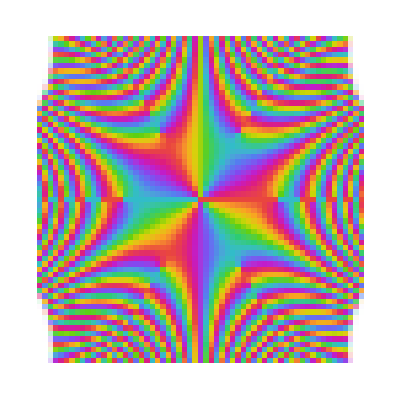

```mathematica
ComplexArrayPlot[Table[Sin[(x+I*y)^3],{y,-3,3,0.1},{x,-3,3,0.1}]]
```

```mathematica
ComplexPlot[Sin[z^3],{z,3}]
```

-Graphics-

If you compare the preceding results, you will notice that they are vertically reflected from each other. This is because the array rows are displayed from the top down, matching how they would be displayed as a matrix.

You can use the DataReversed option to flip the array plot:

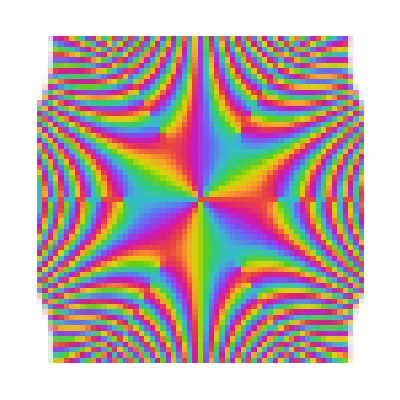

```mathematica
ComplexArrayPlot[Table[Sin[(x+I*y)^3],{y,-3,3,0.1},{x,-3,3,0.1}],DataReversed->True]
```

## New Array Visualization Functions

### RadialAxisPlot

RadialAxisPlot displays an n-dimensional point {x_1,x_2,…,x_n} by putting the coordinate values on axis arranged around a central point:

```mathematica
RadialAxisPlot[{1,2,3,4,5}]
```

-Graphics-

You can compare multiple points by plotting them on the same axes:

```mathematica
RadialAxisPlot[{{1,2,3,4,5},{4,7,3,2,6}}]
```

-Graphics-

You can also use a grid layout for RadialAxisPlot, in which case the axes are kept the same across all the components:

```mathematica
RadialAxisPlot[{{1,2,3,4,5},{4,7,3,2,6}},PlotLayout->"Row"]
```

-Graphics-

If possible, all the axes use the same scale, but you can also allow each axis to be scaled independently:

```mathematica
RadialAxisPlot[{{1,2,3,4,5},{4,7,3,2,6}},PlotRange->All]
```

-Graphics-

The axes are automatically scaled independently if it is clear that there is something different between the axes:

```mathematica
RadialAxisPlot[{1,2,3,4,5},PlotRange->{1->{0,20}}]
```

-Graphics-

As seen, RadialAxisPlot and ParallelAxisPlot extend the specifications for axis-related options like PlotRange, ScalingFunctions, Ticks and AxesLabel to allow a rule-based syntax:

```mathematica
RadialAxisPlot[{1,2,3,4,5},AxesStyle->{_?EvenQ->Red,_->Blue}]
```

-Graphics-

## New Array Visualization Functions

### ParallelAxisPlot

ParallelAxisPlot is similar in concept to RadialAxisPlot, with the main visual difference being that the axes are all parallel to each other, instead of connecting at one central point:

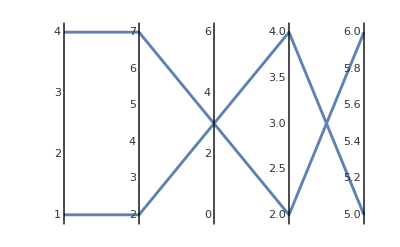

```mathematica
ParallelAxisPlot[{{1,2,3,4,5},{4,7,3,2,6}}]
```

ParallelAxisPlot is read in the same way you would read a ListPlot of a subset of coordinates. In the following example, if you just look at the first two coordinates, the yellow and green points are grouped together and are separate from the blue point. If you look at the last two coordinates, each set of points is separated from the others:

```mathematica
pdata={RandomReal[{1,1.2},{3,5}],RandomReal[{2,2.2},{3,5}],Table[Join[RandomReal[{2,2.2},3],RandomReal[{3,3.2},2]],3]};
```

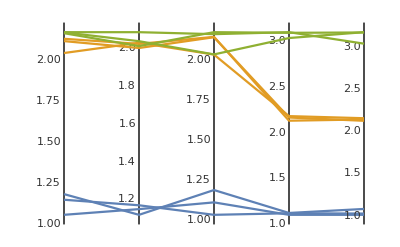

```mathematica
ParallelAxisPlot[pdata]
```

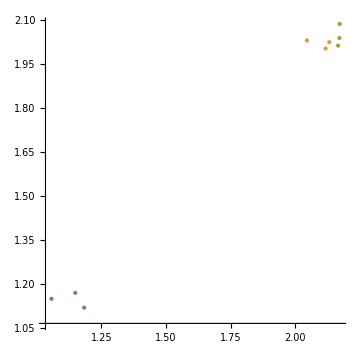
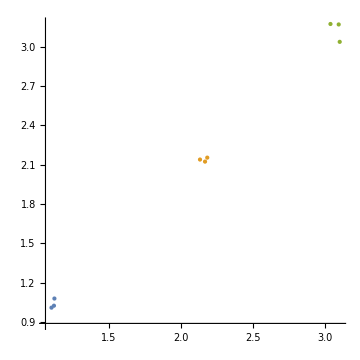

```mathematica
{ListPlot[pdata[[All,All,{1,2}]],],ListPlot[pdata[[All,All,{4,5}]],]}
```

## PointValuePlot

PointValuePlot is a new experimental function that is designed to help make sense of location data that has annotations associated with each location. It tries to make it easy to map the annotation data to visual indicators such as size, color and shape.

In this case, the annotations are mapped to a continuous set of colors:

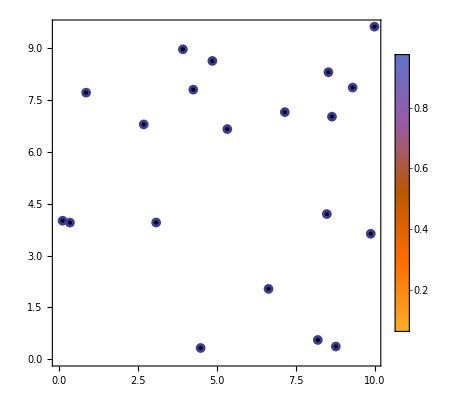

```mathematica
PointValuePlot[Table[RandomReal[10,2]->RandomReal[],20],PlotLegends->Automatic]
```

In this case, there are only a few values, so it uses discrete colors:

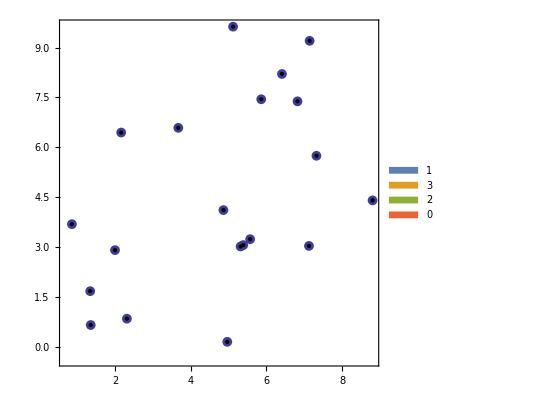

```mathematica
PointValuePlot[Table[RandomReal[10,2]->RandomInteger[3],20],PlotStyle->PointSize[Large],PlotLegends->Automatic]
```

With vectors of numbers, PointValuePlot creates subplots to show the data:

```mathematica
PointValuePlot[Table[RandomReal[10,2]->{RandomReal[],RandomReal[]},20]]
```

-Graphics-

You can also specify how you want different annotations to be visually encoded—in this case, using color and size for the two numeric values:

```mathematica
PointValuePlot[Table[RandomReal[10,2]->{RandomReal[],RandomReal[]},20],{"Color","Size"},PlotLegends->Automatic]
```

-Graphics-

The locations can be geographic as well:

```mathematica
PointValuePlot[Table[RandomGeoPosition[LinguisticAssistant]->RandomReal[100,2],20]]
```

-Graphics-

```mathematica
PointValuePlot[Table[RandomGeoPosition[LinguisticAssistant]->RandomReal[100,2],20],{"Color","Size"},PlotLegends->Automatic]
```

-Graphics-